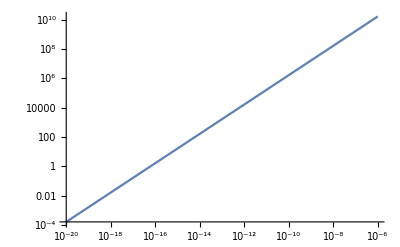

3.42564×10^31

```mathematica
Energy[T_,M_]:=1.6 10^-9  π^2/2(T0(T-T0))/TF M/m/.{m->14 10^6 ,T0->40,TF->.3 10^3  }
ContourPlot[Log10@Energy[T,M],{T,137,.86 10^3},{M,6 10^24,6 10^49},ImageSize->800,PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10"}];
LogLogPlot[Energy[431,M/( 1.8 10^-30)],{M,10^-6(*6 10^24 1.8 10^-30*), 10^-20(*6 10^49 1.8 10^-30*)}]
Energy[860,10^15/( 1.8 10^-30)]
```

```mathematica
Γ == 0.3/(10^30)(3 10^9)^2  100 (3 10^7)"s^-1"
```

Γ==0.0081 s^-1

```mathematica
Quantity[4000,"km"]/Quantity[3 10^9,"cm"]
```

2/15

σ_(them-core)≥2.60308×10^-12 cm^2

(σ/m)_(them-envelope)≥9.28083×10^-41 cm^2/GeV

m_(them-right)==6.05072×10^42 GeV

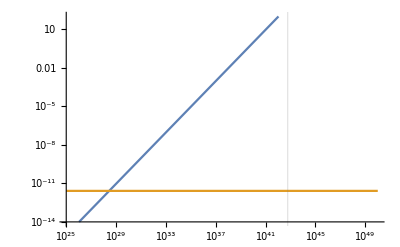

{2.80505×10^28 GeV}

```mathematica
(*9^□Quantity[10^27,"Ergs"]/Quantity[10,"m"](Quantity[10^28,"Centimeters"^-3]Quantity[1,"Megaelectronvolts"] 25)^-1//Simplify//UnitConvert[#,"cm^2"]&*)


Subscript[σ, them-core]≥ (σminthem=Eboom/λT 1/(nion A^4 F^2 mv2)/.{mv2-> Quantity[10,"MeV"], A-> 14,λT-> Quantity[10^-5,"cm"], F-> √0.1,Eboom-> Quantity[10^16,"GeV"],nion-> Quantity[10^31,"cm^-3"]})

Subscript[(σ/m), them-envelope]≥(ThemEnvSlope=(( (0.1 14^4)Quantity[50,"km"]Quantity[10^-3 10^9,"g/cm^3"] Quantity["SpeedOfLight^2"])//N//UnitConvert[#,"GeV/cm^2"]&)^-1)
(*m/σ≥((0.1 (4^4))Quantity[10^35,"cm^-2"]  Quantity[1,"GeV"])//N*)

Subscript[m, them-right]== (mThemRight =( τOLD ρχ RWD^2 focus vhalo)/.{ρχ-> Quantity[.4 ,"GeV/cm^3"],vhalo-> 10^-3 Quantity["c"],τOLD-> Quantity[10^9,"year"],RWD-> Quantity[4000,"km"],focus-> 100}//UnitConvert[#,"GeV"]&)

themPlot=LogLogPlot[{9.28 10^-41 mχ,σminthem},{mχ,10^25,10^50},PlotRange->{10^-14,10^2},GridLines->{{mThemRight/Quantity["GeV"]},{}}]
(mχ/.Solve[Quantity[9.28 10^-41,"cm^2/GeV"] mχ== σminthem,mχ])//UnitConvert[#,"GeV"]&
```

```mathematica
Eboom==(  Quantity[10^28,"ergs"]//UnitConvert[#,"GeV"]&)
```

Eboom==6.241509×10^30 GeV

```mathematica
4^4.1
```

25.6

```mathematica
Subscript[σ, us-core]≥ (σminus=Eboom/λT 1/(nion A^4 F^2 mv2)/.{mv2-> Quantity[10,"MeV"], A-> 4,λT-> Quantity[10,"m"], F-> √0.1,Eboom-> Quantity[10^28,"ergs"],nion-> Quantity[10^26,"cm^-3"]}//UnitConvert[#,"cm^2"]&)

Subscript[(σ/m), us-envelope]≥(UsEnvSlope=(( (0.1 1^4)Quantity[10^35,"cm^-2"]Quantity[1,"GeV"] )//N//UnitConvert[#,"GeV/cm^2"]&)^-1)
(*m/σ≥((0.1 (4^4))Quantity[10^35,"cm^-2"]  Quantity[1,"GeV"])//N*)

Subscript[Γ, us] == ((Γus =  (ρχ/mχ Rcore^2 focus vhalo/.{mχ-> Quantity[10^40,"GeV"],ρχ-> Quantity[.4 ,"GeV/cm^3"],vhalo-> 10^-3 Quantity["c"],τOLD-> Quantity[10^9,"year"],Rcore-> Quantity[3 10^9,"cm"],focus-> 50}//UnitConvert[#,"year^-1"]&))//ScientificForm)
Subscript[m, us-right]== (mUsRight =( τOLD ρχ Rcore^2 focus vhalo)/.{ρχ-> Quantity[.4 ,"GeV/cm^3"],vhalo-> 10^-3 Quantity["c"],τOLD-> Quantity[10^9,"year"],Rcore-> Quantity[3 10^9,"cm"],focus-> 50}//UnitConvert[#,"GeV"]&)

EBoom ≤  (λT^3 nion A^4 F^2 mv2 /.{mv2-> Quantity[10,"MeV"], A-> 4,λT-> Quantity[10,"m"], F-> √0.1,nion-> Quantity[10^26,"cm^-3"]}//UnitConvert[#,"GeV"]&)
usPlot=LogLogPlot[{UsEnvSlope mχ,σminus},{mχ,10^25,10^50},PlotRange->{10^-14,10^12},GridLines->{{mUsRight/Quantity["GeV"]},{}},ImageSize->800,Frame-> True,FrameStyle->Directive[FontSize-> 25]];
(mχ/.Solve[Quantity[9.28 10^-41,"cm^2/GeV"] mχ== σminthem,mχ])//UnitConvert[#,"GeV"]&
focus ==(((2 Quantity["G"] Quantity[0.5,"SolarMass"])/(Quantity[10^-3,"c"]^2 Quantity[3 10^9,"cm"])))
```

σ_(us-core)≥243.809 cm^2

(σ/m)_(us-envelope)≥1.×10^-34 cm^2/GeV

Γ_us==1.70177×10^-5 per year

m_(us-right)==1.70177×10^44 GeV

EBoom≤2.56×10^34 GeV

{2.80505×10^28 GeV}

focus==49.2198

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

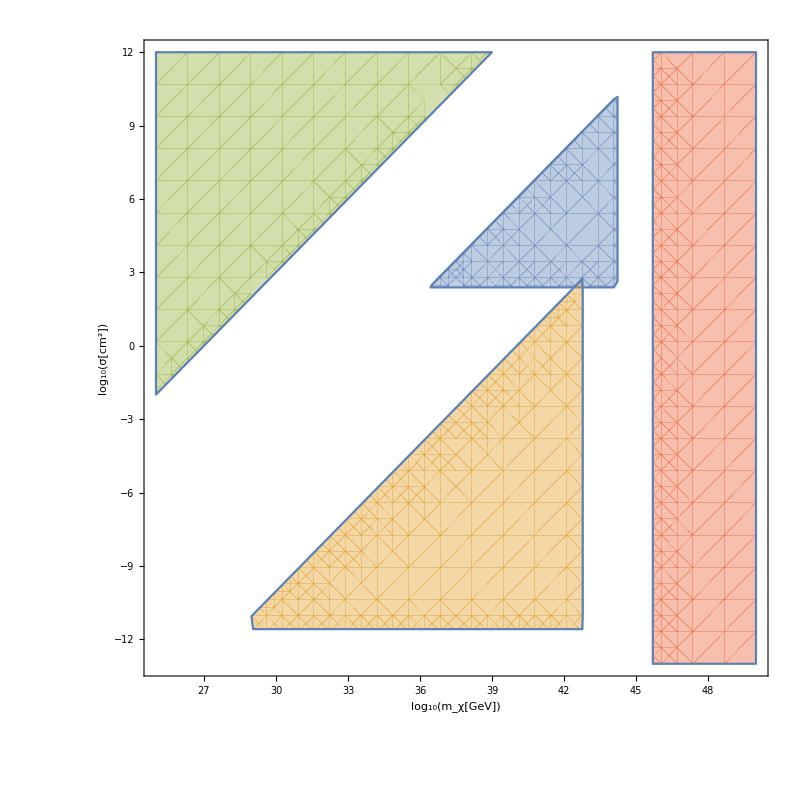

```mathematica
colors=ColorData[97,"ColorList"]
usRegion=RegionPlot[(σ≤ UsEnvSlope  Quantity["GeV/cm^2"] mχ && σ ≥ σminus Quantity["cm^-2"]  && mχ ≤ mUsRight Quantity["GeV^-1"] )/.{σ-> 10^logσ,mχ-> 10^logmχ} ,{logmχ,25,50},{logσ,-13,12},PlotStyle->Directive[colors[[1]],Opacity[0.4]],Frame-> True,FrameLabel->{{"log_10(σ[cm^2])",""},{"log_10(m_χ[GeV])",""}},ImageSize->800,FrameStyle->Directive[FontSize-> 25],PlotRangePadding->0];
themRegion=RegionPlot[(σ≤ ThemEnvSlope  Quantity["GeV/cm^2"] mχ && σ ≥ σminthem Quantity["cm^-2"]  && mχ ≤ mThemRight Quantity["GeV^-1"] )/.{σ-> 10^logσ,mχ-> 10^logmχ} ,{logmχ,25,50},{logσ,-13,12},PlotStyle->Directive[colors[[2]],Opacity[0.4]]];
CMBRegion=RegionPlot[(σ≥  10^-27 mχ )/.{σ-> 10^logσ,mχ-> 10^logmχ} ,{logmχ,25,50},{logσ,-13,12},PlotStyle->Directive[colors[[3]],Opacity[0.4]]];
SubaruRegion=RegionPlot[(mχ≥5 10^45  )/.{σ-> 10^logσ,mχ-> 10^logmχ} ,{logmχ,25,50},{logσ,-13,12},PlotStyle->Directive[colors[[4]],Opacity[0.4]]];
Show[usRegion,themRegion,CMBRegion,SubaruRegion]
```

## DM Capture in RG star

```mathematica
t1[mχ_,σχA_] := (mχ/mion)^(3/2) Rstar/vesc 1/Nscat 1/(√Max[Nscat,1])//.{mion-> Quantity["GeV"],Rstar-> 3 10^10 Quantity["m"],nion -> Quantity[10^35,"cm^-2"]/Rstar,vesc-> vhalo √f,vhalo-> 10^-3 Quantity["c"],f-> 50,Nscat-> σχA nion Rstar}
t1[mχ_,σχA_] := (mχ/mion)^(3/2) Rstar/vesc 1/Nscat 1/(√Nscat)//.{mion-> Quantity["GeV"],Rstar-> 3 10^10 Quantity["m"],nion -> Quantity[10^35,"cm^-2"]/Rstar,vesc-> vhalo √f,vhalo-> 10^-3 Quantity["c"],f-> 50,Nscat-> σχA nion Rstar}
t1[10^30 Quantity["GeV"],σχn .1 1^4/.{σχn-> (10^-35 Quantity["cm"]^2)/(.1 14^4)}]//UnitConvert[#,"years"]&
```

3.37891×10^48 yr